```mathematica
Quit[];
```

```mathematica
AppendTo[$Path,"~/RHPackage"];
<<RiemannHilbert`;
bt[k_,U0_]:=1/2-I k-(U0+1/4)^(1/2);
at[k_,U0_]:=1/2-I k+(U0+1/4)^(1/2);
ct[k_,U0_]:=1-I k;
a[k_,U0_]:=(Gamma[at[k,U0]] Gamma[bt[k,U0]])/(Gamma[ct[k,U0]] Gamma[at[k,U0]+bt[k,U0]-ct[k,U0]]);
r[_?ZeroQ,_]:=-1;
r[k_,U0_]:=(a[k,U0] Gamma[ct[k,U0]]Gamma[ct[k,U0]-at[k,U0]-bt[k,U0]])/(Gamma[ct[k,U0]-at[k,U0]] Gamma[ct[k,U0]-bt[k,U0]]);
sp[x_]:=SetPrecision[x,400];
data=Import["~/points.txt",{"Lines"}];
points = sp/@ToExpression/@data;
U0 = -1//sp;
reflection = Table[r[points[[i]],U0] ,{i,1,Length[points]}];
datagrid = {Re[reflection],Im[reflection]}//Transpose;
Export["~/reflection_re.txt",Re[reflection]]
Export["~/reflection_im.txt",Im[reflection]]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

~/reflection_re.txt

~/reflection_im.txt

```mathematica
Length[reflection]
```

4096

```mathematica
Tan[-Pi/2]
```

ComplexInfinity

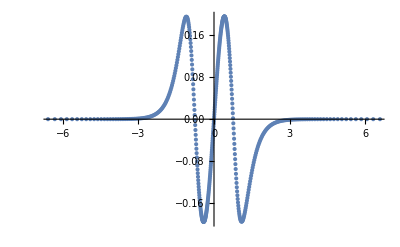

```mathematica
ListPlot[{points,reflection//Im}//Transpose]
```

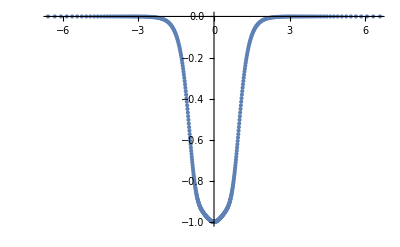

```mathematica
ListPlot[{points,reflection//Re}//Transpose]
```

```mathematica
x[j_]:=Tan[(Pi/2)*q[j]];
q[j_]:=2*(j/NN)-1;
```

```mathematica
NN = 1024
Table[x[j],{j,1,NN-1}]//N
```

1024

{-325.948,-162.973,-108.647,-81.4832,-65.1848,-54.3188,-46.557,-40.7355,-36.2074,-32.5847,-29.6205,-27.1502,-25.0597,-23.2678,-21.7146,-20.3555,-19.1561,-18.0899,-17.1358,-16.277,-15.4999,-14.7934,-14.1482,-13.5567,-13.0124,-12.5099,-12.0446,-11.6124,-11.21,-10.8343,-10.4828,-10.1532,-9.84348,-9.55195,-9.27702,-9.0173,-8.77157,-8.53872,-8.31775,-8.10779,-7.90801,-7.7177,-7.53619,-7.36289,-7.19724,-7.03875,-6.88696,-6.74145,-6.60184,-6.46777,-6.33892,-6.21499,-6.09569,-5.98077,-5.87,-5.76314,-5.66,-5.56038,-5.4641,-5.37099,-5.2809,-5.19369,-5.10921,-5.02734,-4.94796,-4.87095,-4.7962,-4.72363,-4.65313,-4.58461,-4.518,-4.4532,-4.39015,-4.32878,-4.26902,-4.2108,-4.15407,-4.09876,-4.04483,-3.99222,-3.94089,-3.89078,-3.84185,-3.79406,-3.74738,-3.70175,-3.65715,-3.61354,-3.57088,-3.52915,-3.48831,-3.44834,-3.4092,-3.37088,-3.33334,-3.29656,-3.26051,-3.22518,-3.19055,-3.15658,-3.12327,-3.09058,-3.05852,-3.02704,-2.99615,-2.96582,-2.93604,-2.90679,-2.87805,-2.84982,-2.82208,-2.79481,-2.76801,-2.74166,-2.71575,-2.69027,-2.6652,-2.64054,-2.61628,-2.5924,-2.5689,-2.54577,-2.523,-2.50057,-2.47849,-2.45674,-2.43532,-2.41421,-2.39342,-2.37293,-2.35273,-2.33282,-2.3132,-2.29385,-2.27478,-2.25596,-2.23741,-2.21911,-2.20106,-2.18325,-2.16567,-2.14833,-2.13121,-2.11432,-2.09765,-2.08119,-2.06493,-2.04889,-2.03304,-2.01739,-2.00193,-1.98666,-1.97157,-1.95667,-1.94195,-1.92739,-1.91301,-1.8988,-1.88475,-1.87087,-1.85714,-1.84357,-1.83015,-1.81688,-1.80376,-1.79078,-1.77794,-1.76525,-1.75269,-1.74026,-1.72797,-1.7158,-1.70377,-1.69186,-1.68007,-1.6684,-1.65685,-1.64542,-1.6341,-1.6229,-1.6118,-1.60082,-1.58994,-1.57917,-1.56851,-1.55794,-1.54748,-1.53711,-1.52684,-1.51667,-1.50659,-1.49661,-1.48671,-1.47691,-1.46719,-1.45756,-1.44802,-1.43856,-1.42918,-1.41989,-1.41068,-1.40154,-1.39249,-1.38351,-1.37461,-1.36578,-1.35703,-1.34834,-1.33973,-1.33119,-1.32272,-1.31432,-1.30599,-1.29772,-1.28952,-1.28138,-1.27331,-1.2653,-1.25735,-1.24946,-1.24163,-1.23386,-1.22616,-1.2185,-1.21091,-1.20337,-1.19589,-1.18846,-1.18108,-1.17376,-1.16649,-1.15928,-1.15211,-1.145,-1.13793,-1.13092,-1.12395,-1.11703,-1.11016,-1.10333,-1.09655,-1.08982,-1.08313,-1.07648,-1.06988,-1.06332,-1.05681,-1.05033,-1.0439,-1.03751,-1.03116,-1.02485,-1.01858,-1.01235,-1.00615,-1.,-0.993883,-0.987803,-0.98176,-0.975753,-0.969782,-0.963846,-0.957945,-0.952079,-0.946247,-0.940449,-0.934684,-0.928952,-0.923253,-0.917586,-0.911951,-0.906347,-0.900774,-0.895232,-0.889721,-0.884239,-0.878787,-0.873365,-0.867971,-0.862606,-0.857269,-0.851961,-0.84668,-0.841426,-0.836199,-0.830999,-0.825826,-0.820679,-0.815557,-0.810462,-0.805391,-0.800345,-0.795325,-0.790328,-0.785356,-0.780408,-0.775483,-0.770582,-0.765703,-0.760848,-0.756015,-0.751205,-0.746417,-0.741651,-0.736906,-0.732183,-0.72748,-0.722799,-0.718139,-0.713499,-0.708879,-0.704279,-0.6997,-0.695139,-0.690599,-0.686077,-0.681574,-0.677091,-0.672625,-0.668179,-0.66375,-0.659339,-0.654947,-0.650571,-0.646214,-0.641873,-0.63755,-0.633243,-0.628953,-0.62468,-0.620423,-0.616182,-0.611957,-0.607748,-0.603555,-0.599377,-0.595214,-0.591067,-0.586935,-0.582817,-0.578715,-0.574626,-0.570553,-0.566493,-0.562448,-0.558416,-0.554398,-0.550394,-0.546403,-0.542426,-0.538462,-0.534511,-0.530573,-0.526648,-0.522735,-0.518835,-0.514948,-0.511072,-0.507209,-0.503358,-0.499518,-0.495691,-0.491875,-0.48807,-0.484277,-0.480495,-0.476724,-0.472965,-0.469216,-0.465478,-0.461751,-0.458034,-0.454327,-0.450631,-0.446945,-0.44327,-0.439604,-0.435948,-0.432302,-0.428665,-0.425038,-0.421421,-0.417812,-0.414214,-0.410624,-0.407043,-0.403471,-0.399908,-0.396354,-0.392808,-0.389271,-0.385743,-0.382222,-0.37871,-0.375206,-0.37171,-0.368223,-0.364743,-0.36127,-0.357806,-0.354349,-0.350899,-0.347457,-0.344023,-0.340595,-0.337175,-0.333762,-0.330355,-0.326956,-0.323563,-0.320178,-0.316799,-0.313426,-0.31006,-0.3067,-0.303347,-0.3,-0.296659,-0.293324,-0.289995,-0.286672,-0.283354,-0.280043,-0.276737,-0.273437,-0.270143,-0.266853,-0.26357,-0.260291,-0.257018,-0.25375,-0.250487,-0.247229,-0.243976,-0.240728,-0.237484,-0.234246,-0.231012,-0.227782,-0.224558,-0.221337,-0.218121,-0.214909,-0.211702,-0.208498,-0.205299,-0.202104,-0.198912,-0.195725,-0.192541,-0.189362,-0.186185,-0.183013,-0.179844,-0.176678,-0.173516,-0.170358,-0.167202,-0.16405,-0.160901,-0.157756,-0.154613,-0.151473,-0.148336,-0.145202,-0.142071,-0.138942,-0.135816,-0.132693,-0.129572,-0.126454,-0.123338,-0.120225,-0.117114,-0.114005,-0.110898,-0.107793,-0.104691,-0.10159,-0.0984914,-0.0953946,-0.0922996,-0.0892064,-0.0861149,-0.0830249,-0.0799366,-0.0768498,-0.0737644,-0.0706805,-0.0675978,-0.0645165,-0.0614364,-0.0583574,-0.0552795,-0.0522027,-0.0491268,-0.0460519,-0.0429779,-0.0399047,-0.0368322,-0.0337604,-0.0306892,-0.0276187,-0.0245486,-0.021479,-0.0184098,-0.015341,-0.0122725,-0.00920414,-0.006136,-0.00306797,0.,0.00306797,0.006136,0.00920414,0.0122725,0.015341,0.0184098,0.021479,0.0245486,0.0276187,0.0306892,0.0337604,0.0368322,0.0399047,0.0429779,0.0460519,0.0491268,0.0522027,0.0552795,0.0583574,0.0614364,0.0645165,0.0675978,0.0706805,0.0737644,0.0768498,0.0799366,0.0830249,0.0861149,0.0892064,0.0922996,0.0953946,0.0984914,0.10159,0.104691,0.107793,0.110898,0.114005,0.117114,0.120225,0.123338,0.126454,0.129572,0.132693,0.135816,0.138942,0.142071,0.145202,0.148336,0.151473,0.154613,0.157756,0.160901,0.16405,0.167202,0.170358,0.173516,0.176678,0.179844,0.183013,0.186185,0.189362,0.192541,0.195725,0.198912,0.202104,0.205299,0.208498,0.211702,0.214909,0.218121,0.221337,0.224558,0.227782,0.231012,0.234246,0.237484,0.240728,0.243976,0.247229,0.250487,0.25375,0.257018,0.260291,0.26357,0.266853,0.270143,0.273437,0.276737,0.280043,0.283354,0.286672,0.289995,0.293324,0.296659,0.3,0.303347,0.3067,0.31006,0.313426,0.316799,0.320178,0.323563,0.326956,0.330355,0.333762,0.337175,0.340595,0.344023,0.347457,0.350899,0.354349,0.357806,0.36127,0.364743,0.368223,0.37171,0.375206,0.37871,0.382222,0.385743,0.389271,0.392808,0.396354,0.399908,0.403471,0.407043,0.410624,0.414214,0.417812,0.421421,0.425038,0.428665,0.432302,0.435948,0.439604,0.44327,0.446945,0.450631,0.454327,0.458034,0.461751,0.465478,0.469216,0.472965,0.476724,0.480495,0.484277,0.48807,0.491875,0.495691,0.499518,0.503358,0.507209,0.511072,0.514948,0.518835,0.522735,0.526648,0.530573,0.534511,0.538462,0.542426,0.546403,0.550394,0.554398,0.558416,0.562448,0.566493,0.570553,0.574626,0.578715,0.582817,0.586935,0.591067,0.595214,0.599377,0.603555,0.607748,0.611957,0.616182,0.620423,0.62468,0.628953,0.633243,0.63755,0.641873,0.646214,0.650571,0.654947,0.659339,0.66375,0.668179,0.672625,0.677091,0.681574,0.686077,0.690599,0.695139,0.6997,0.704279,0.708879,0.713499,0.718139,0.722799,0.72748,0.732183,0.736906,0.741651,0.746417,0.751205,0.756015,0.760848,0.765703,0.770582,0.775483,0.780408,0.785356,0.790328,0.795325,0.800345,0.805391,0.810462,0.815557,0.820679,0.825826,0.830999,0.836199,0.841426,0.84668,0.851961,0.857269,0.862606,0.867971,0.873365,0.878787,0.884239,0.889721,0.895232,0.900774,0.906347,0.911951,0.917586,0.923253,0.928952,0.934684,0.940449,0.946247,0.952079,0.957945,0.963846,0.969782,0.975753,0.98176,0.987803,0.993883,1.,1.00615,1.01235,1.01858,1.02485,1.03116,1.03751,1.0439,1.05033,1.05681,1.06332,1.06988,1.07648,1.08313,1.08982,1.09655,1.10333,1.11016,1.11703,1.12395,1.13092,1.13793,1.145,1.15211,1.15928,1.16649,1.17376,1.18108,1.18846,1.19589,1.20337,1.21091,1.2185,1.22616,1.23386,1.24163,1.24946,1.25735,1.2653,1.27331,1.28138,1.28952,1.29772,1.30599,1.31432,1.32272,1.33119,1.33973,1.34834,1.35703,1.36578,1.37461,1.38351,1.39249,1.40154,1.41068,1.41989,1.42918,1.43856,1.44802,1.45756,1.46719,1.47691,1.48671,1.49661,1.50659,1.51667,1.52684,1.53711,1.54748,1.55794,1.56851,1.57917,1.58994,1.60082,1.6118,1.6229,1.6341,1.64542,1.65685,1.6684,1.68007,1.69186,1.70377,1.7158,1.72797,1.74026,1.75269,1.76525,1.77794,1.79078,1.80376,1.81688,1.83015,1.84357,1.85714,1.87087,1.88475,1.8988,1.91301,1.92739,1.94195,1.95667,1.97157,1.98666,2.00193,2.01739,2.03304,2.04889,2.06493,2.08119,2.09765,2.11432,2.13121,2.14833,2.16567,2.18325,2.20106,2.21911,2.23741,2.25596,2.27478,2.29385,2.3132,2.33282,2.35273,2.37293,2.39342,2.41421,2.43532,2.45674,2.47849,2.50057,2.523,2.54577,2.5689,2.5924,2.61628,2.64054,2.6652,2.69027,2.71575,2.74166,2.76801,2.79481,2.82208,2.84982,2.87805,2.90679,2.93604,2.96582,2.99615,3.02704,3.05852,3.09058,3.12327,3.15658,3.19055,3.22518,3.26051,3.29656,3.33334,3.37088,3.4092,3.44834,3.48831,3.52915,3.57088,3.61354,3.65715,3.70175,3.74738,3.79406,3.84185,3.89078,3.94089,3.99222,4.04483,4.09876,4.15407,4.2108,4.26902,4.32878,4.39015,4.4532,4.518,4.58461,4.65313,4.72363,4.7962,4.87095,4.94796,5.02734,5.10921,5.19369,5.2809,5.37099,5.4641,5.56038,5.66,5.76314,5.87,5.98077,6.09569,6.21499,6.33892,6.46777,6.60184,6.74145,6.88696,7.03875,7.19724,7.36289,7.53619,7.7177,7.90801,8.10779,8.31775,8.53872,8.77157,9.0173,9.27702,9.55195,9.84348,10.1532,10.4828,10.8343,11.21,11.6124,12.0446,12.5099,13.0124,13.5567,14.1482,14.7934,15.4999,16.277,17.1358,18.0899,19.1561,20.3555,21.7146,23.2678,25.0597,27.1502,29.6205,32.5847,36.2074,40.7355,46.557,54.3188,65.1848,81.4832,108.647,162.973,325.948}